```mathematica
Solve[a+x^2(1/2-2a^2) h v==0,a]
```

{{a→(1-√(1+4 h^2 v^2 x^4))/(4 h v x^2)},{a→(1+√(1+4 h^2 v^2 x^4))/(4 h v x^2)}}

```mathematica
NIntegrate[-x^2+1,{x,0,1}]
```

0.666667

```mathematica
-1/2D[Exp[-a z^2],{z,2}]+z^2/2Exp[-a z^2]
Simplify@%
```

1/2 ⅇ^(-a z^2) z^2+1/2 (2 a ⅇ^(-a z^2)-4 a^2 ⅇ^(-a z^2) z^2)

1/2 ⅇ^(-a z^2) (2 a+z^2-4 a^2 z^2)

```mathematica
Exp[-α*(z^2)]*(-0.5*D[Exp[-α*z^2], {z, 2}] + 0.5*z^2*Exp[-α*z^2])
Abs[Exp[(-α*(z^2))]]^2
```

ⅇ^(-z^2 α) (0.5 ⅇ^(-z^2 α) z^2-0.5 (-2 ⅇ^(-z^2 α) α+4 ⅇ^(-z^2 α) z^2 α^2))

ⅇ^(-2 Re[z^2 α])

```mathematica
α=1/2;
NIntegrate[ⅇ^(-z^2 α) (0.5 ⅇ^(-z^2 α) z^2-0.5 (-2 ⅇ^(-z^2 α) α+4 ⅇ^(-z^2 α) z^2 α^2)),
{z,-2,2}]/NIntegrate[ⅇ^(-2 Re[z^2 α]),
{z,-2,2}]
Clear[α];
```

0.5

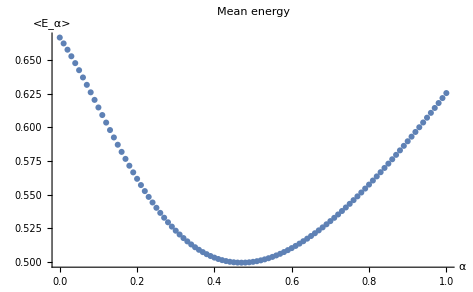

```mathematica
a=Table[NIntegrate[ⅇ^(-z^2 α) (0.5 ⅇ^(-z^2 α) z^2-0.5 (-2 ⅇ^(-z^2 α) α+4 ⅇ^(-z^2 α) z^2 α^2)),
{z,-2,2}]/NIntegrate[ⅇ^(-2 Re[z^2 α]),
{z,-2,2}]
,{α,0,1,0.01}];
ListPlot[a,DataRange->{0,1},PlotRange->All,PlotLabel->"Mean energy",AxesLabel->{"α","<E_α>"}]
```

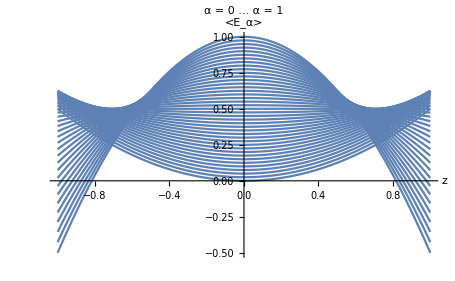

```mathematica
a=Plot[Table[alpha+z^2(1/2-2alpha^2),{alpha,0,1,0.025}],{z,-1,1},PlotLabel->"α = 0 ... α = 1",AxesLabel->{"z","<E_α>"}]
Show[a,PlotRange->{-1.25,1.25}];
```

```mathematica
r = Sqrt[(x1^2+x2^2)^2+(y1^2+y2^2)^2]
ψ =Exp[-(x1^2+x2^2+y1^2+y2^2)/2]*Exp[λ r/(1+α r)]
en = -1/2(D[ψ,{x1,2}]+D[ψ,{x2,2}]+D[ψ,{y1,2}]+D[ψ,{y2,2}])+1/2(x1^2+x2^2+y1^2+y2^2)ψ+λ/r ψ
```

1

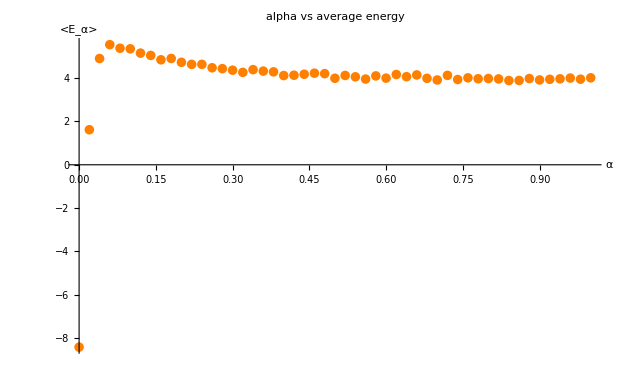

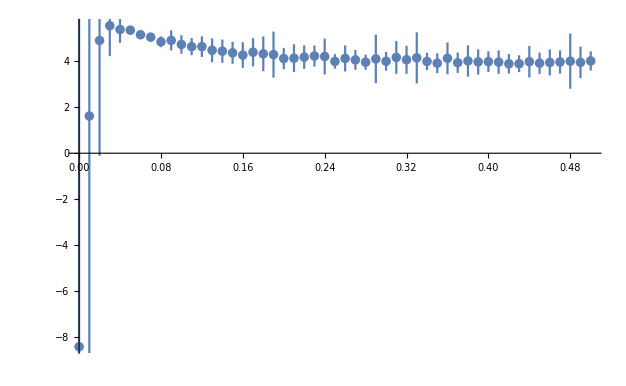

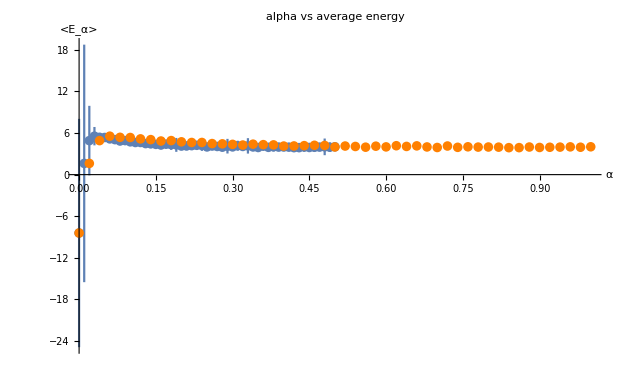

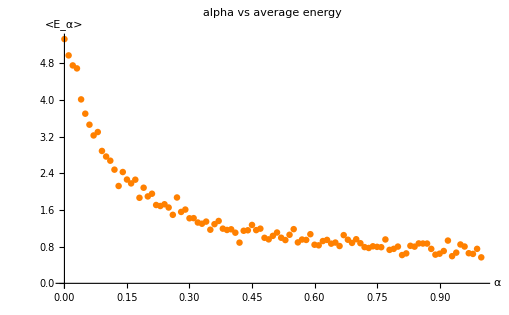

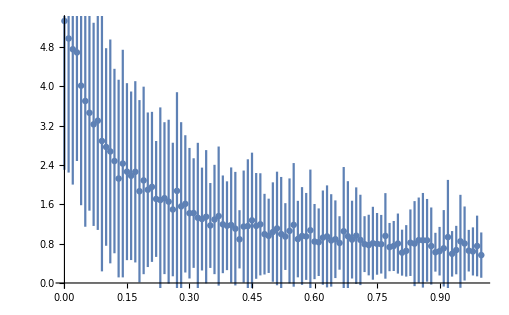

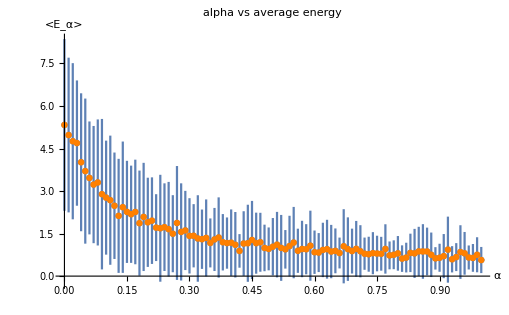

```mathematica
Needs["ErrorBarPlots`"];
list = Import["~/phd-stuff/courses/comp_phys/analysis.csv"];
alphalist = Table[list[[i]][[1]],{i,1,Length[list]}];
b=ListPlot[alphalist,PlotRange->All,PlotStyle->Orange,DataRange->{0,1},PlotLabel->"alpha vs average energy",PlotRange->All,AxesLabel->{"α","<E_α>"}]
errorlist = Table[list[[i]][[2]],{i,1,Length[list]}];
errorlistplot = Table[{{i/100-1/100,alphalist[[i]]},ErrorBar[errorlist[[i]]]},{i,1,Length[list]}];
a=ErrorListPlot[errorlistplot,PlotRange->All]
Show[a,b,PlotLabel->"alpha vs average energy",AxesLabel->{"α","<E_α>"},PlotRange->All]
```

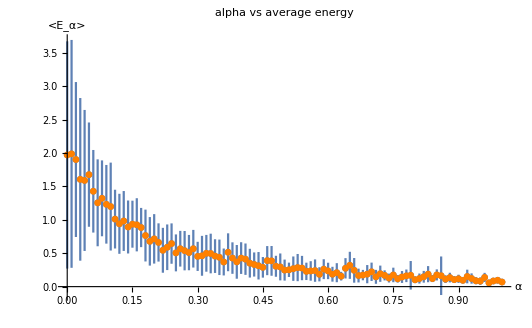

```mathematica
Length[list]
```

20